## Package préalable :

```mathematica
tc=1200.  Log[2,2187/2048];td=1200. Log[2,256/243];T=tc+td;Q=3tc+4td;
intervMAJencents={0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td};
doremifasollasiPyth=Most[Accumulate[intervMAJencents]]//N;
noteschromatiques=Table[100k,{k,0,11}];
doremifasollasiChrom={0,200,400,500,700,900,1100};

theta[s_]:=Mod[(300.-s)/300. π/2,2π]           (*Cette fonction donne l'angle trigonométrique quand on donne l'écart en cents par rapport au sommet du cercle parcouru dans le sens horlogique*)
notes12={"do=si♯","ré♭=do♯","ré","mi♭=ré♯","mi=fa♭","fa=mi♯","sol♭=fa♯","sol","la♭=sol♯","la","si♭=la♯","si=do♭"}
modesmajeurs={"do Majeur","si♯ Majeur","ré♭ Majeur","do♯ Majeur","ré Majeur","mi♭ Majeur","ré♯ Majeur","fa♭ Majeur","mi Majeur","fa Majeur","mi♯ Majeur","sol♭ Majeur","fa♯ Majeur","sol Majeur","la♭ Majeur","sol♯ Majeur","la Majeur","si♭ Majeur","la♯ Majeur","do♭ Majeur","si Majeur"};
notes21={"do","si♯","ré♭","do♯","ré","mi♭","ré♯","fa♭","mi","fa","mi♯","sol♭","fa♯","sol","la♭","sol♯","la","si♭","la♯","do♭","si"};
notesdebase=Most[Accumulate[{0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td}]];
touteslesnotes21=Sort[Union[Join[N[notesdebase],Mod[N[notesdebase]+tc,1200],Mod[N[notesdebase]-tc,1200]]]];
touteslesnotes35=Union[Join[touteslesnotes21,Mod[touteslesnotes21+tc,1200],Mod[touteslesnotes21-tc,1200]]];
notes35={"do","si ♯","ré ♭","do ♯","si ♯♯","mi ♭♭","ré","do ♯♯","fa ♭♭","mi ♭","ré ♯","fa ♭","mi","ré ♯♯","sol ♭♭","fa","mi ♯","sol ♭","fa ♯","mi ♯♯","la ♭♭","sol","fa ♯♯","la ♭","sol ♯","si ♭♭","la","sol ♯♯","do ♭♭","si ♭","la ♯","do ♭","si","la ♯♯","ré ♭♭"};
notes35quintes={"fa ♭♭","do ♭♭","sol ♭♭","ré ♭♭","la ♭♭","mi ♭♭","si ♭♭","fa ♭","do ♭","sol ♭","ré ♭","la ♭","mi ♭","si ♭","fa","do","sol","ré","la","mi","si","fa ♯","do ♯","sol ♯","ré ♯","la ♯","mi ♯","si ♯","fa ♯♯","do ♯♯","sol ♯♯","ré ♯♯","la ♯♯","mi ♯♯","si ♯♯"};
notes21quintes={"fa♭","do♭","sol♭","ré♭","la♭","mi♭","si♭","fa","do","sol","ré","la","mi","si","fa♯","do♯","sol♯","ré♯","la♯","mi♯","si♯"};
```

{do=si♯,ré♭=do♯,ré,mi♭=ré♯,mi=fa♭,fa=mi♯,sol♭=fa♯,sol,la♭=sol♯,la,si♭=la♯,si=do♭}

## Gamme de Zarlino simplifiée en négligeant les anharmonies et les schismas

```mathematica
Grid[Table[(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]]),{n,-1,2},{m,-1,2}],Frame->All]
```

16/15 | 8/5 | 6/5 | 9/5
4/3 | 1 | 3/2 | 9/8
5/3 | 5/4 | 15/8 | 45/32
25/24 | 25/16 | 75/64 | 225/128

```mathematica
Grid[Table[Column[{notes21quintes[[m+4n+6]],(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]]),1200.Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])]},Center],{n,-1,2},{m,-1,2}],Frame->All,Background->{None,None,{{2,2}->Pink,{3,2}->Pink,{2,3}->Pink}}]
```

fa♭
16/15
111.731 | do♭
8/5
813.686 | sol♭
6/5
315.641 | ré♭
9/5
1017.6
la♭
4/3
498.045 | mi♭
1
0. | si♭
3/2
701.955 | fa
9/8
203.91
do
5/3
884.359 | sol
5/4
386.314 | ré
15/8
1088.27 | la
45/32
590.224
mi
25/24
70.6724 | si
25/16
772.627 | fa♯
75/64
274.582 | do♯
225/128
976.537

```mathematica
Sort[Drop[Drop[Flatten[Table[Column[{notes35quintes[[m+4n+16]],(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]]),1200.Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])]},Center],{n,-2,3},{m,-2,3}]],{1,2}],{32,34}]](*Notes zarliniennes sans les altérations doubles*)
```

{do
1
0.,do ♭
48/25
1129.33,do ♯
25/24
70.6724,do ♯
135/128
92.1787,fa
4/3
498.045,fa
27/20
519.551,fa ♭
32/25
427.373,fa ♯
25/18
568.717,fa ♯
45/32
590.224,la
5/3
884.359,la
27/16
905.865,la ♭
8/5
813.686,la ♯
125/72
955.031,la ♯
225/128
976.537,mi
5/4
386.314,mi ♭
6/5
315.641,mi ♯
125/96
456.986,mi ♯
675/512
478.492,ré
10/9
182.404,ré
9/8
203.91,ré ♭
16/15
111.731,ré ♭
27/25
133.238,ré ♯
75/64
274.582,si
15/8
1088.27,si ♭
16/9
996.09,si ♭
9/5
1017.6,si ♯
125/64
1158.94,sol
3/2
701.955,sol ♭
64/45
609.776,sol ♭
36/25
631.283,sol ♯
25/16
772.627}

```mathematica
Sort[Drop[Drop[Flatten[Table[{notes35quintes[[m+4n+16]],(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]]),1200.Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])]},{n,-2,3},{m,-2,3}],1],{1,2}],{32,34}],#1[[3]]<#2[[3]]&]                       (*Notes zarliniennes sans les altérations doubles : 31 notes là où il n'y en a que 21 chez Pythagore et 12 en tempéré*)
```

{{do,1,0.},{do ♯,25/24,70.6724},{do ♯,135/128,92.1787},{ré ♭,16/15,111.731},{ré ♭,27/25,133.238},{ré,10/9,182.404},{ré,9/8,203.91},{ré ♯,75/64,274.582},{mi ♭,6/5,315.641},{mi,5/4,386.314},{fa ♭,32/25,427.373},{mi ♯,125/96,456.986},{mi ♯,675/512,478.492},{fa,4/3,498.045},{fa,27/20,519.551},{fa ♯,25/18,568.717},{fa ♯,45/32,590.224},{sol ♭,64/45,609.776},{sol ♭,36/25,631.283},{sol,3/2,701.955},{sol ♯,25/16,772.627},{la ♭,8/5,813.686},{la,5/3,884.359},{la,27/16,905.865},{la ♯,125/72,955.031},{la ♯,225/128,976.537},{si ♭,16/9,996.09},{si ♭,9/5,1017.6},{si,15/8,1088.27},{do ♭,48/25,1129.33},{si ♯,125/64,1158.94}}

```mathematica
Grid[Table[Column[{notes35quintes[[m+4n+16]],(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]]),1200.Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])]},Center],{n,-2,3},{m,-2,3}],Frame->All,Background->{None,None,{{3,3}->Pink,{3,4}->Pink,{4,3}->Pink}}]
```

mi ♭♭
256/225
223.463 | si ♭♭
128/75
925.418 | fa ♭
32/25
427.373 | do ♭
48/25
1129.33 | sol ♭
36/25
631.283 | ré ♭
27/25
133.238
sol ♭
64/45
609.776 | ré ♭
16/15
111.731 | la ♭
8/5
813.686 | mi ♭
6/5
315.641 | si ♭
9/5
1017.6 | fa
27/20
519.551
si ♭
16/9
996.09 | fa
4/3
498.045 | do
1
0. | sol
3/2
701.955 | ré
9/8
203.91 | la
27/16
905.865
ré
10/9
182.404 | la
5/3
884.359 | mi
5/4
386.314 | si
15/8
1088.27 | fa ♯
45/32
590.224 | do ♯
135/128
92.1787
fa ♯
25/18
568.717 | do ♯
25/24
70.6724 | sol ♯
25/16
772.627 | ré ♯
75/64
274.582 | la ♯
225/128
976.537 | mi ♯
675/512
478.492
la ♯
125/72
955.031 | mi ♯
125/96
456.986 | si ♯
125/64
1158.94 | fa ♯♯
375/256
660.896 | do ♯♯
1125/1024
162.851 | sol ♯♯
3375/2048
864.806

```mathematica
zarl16=Flatten[Table[1200. Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])],{n,-1,2},{m,-1,2}]]
```

{111.731,813.686,315.641,1017.6,498.045,0.,701.955,203.91,884.359,386.314,1088.27,590.224,70.6724,772.627,274.582,976.537}

```mathematica
zarl16ordonne=Sort[Flatten[Table[1200. Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])],{n,-1,2},{m,-1,2}]]]
```

{0.,70.6724,111.731,203.91,274.582,315.641,386.314,498.045,590.224,701.955,772.627,813.686,884.359,976.537,1017.6,1088.27}

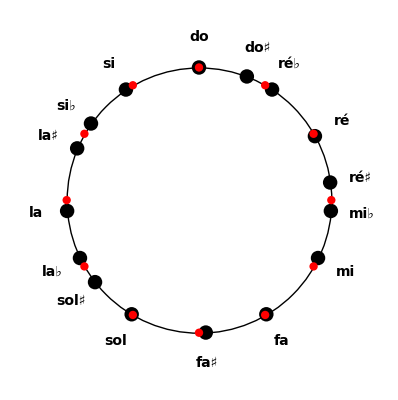

```mathematica
zarlino16=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21quintes[[k]],Bold,FontSize->14],{(3.7+If[k==12,0,0]+If[k==13,0,0])Cos[theta[zarl16[[k-3]]]],3.7Sin[theta[zarl16[[k-3]]]]}],{k,4,19}],Table[Point[{3Cos[theta[zarl16[[k]]]],3Sin[theta[zarl16[[k]]]]}],{k,1,16}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

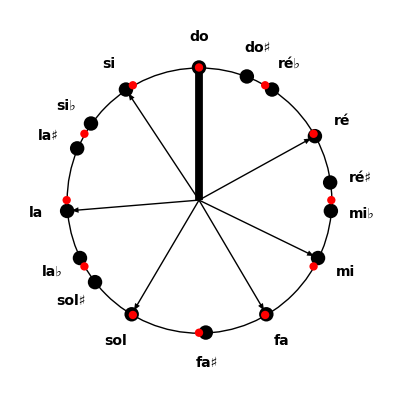

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21quintes[[k]],Bold,FontSize->14],{(3.7+If[k==12,0,0]+If[k==13,0,0])Cos[theta[zarl16[[k-3]]]],3.7Sin[theta[zarl16[[k-3]]]]}],{k,4,19}],Table[Point[{3Cos[theta[zarl16[[k]]]],3Sin[theta[zarl16[[k]]]]}],{k,1,16}],Table[Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[k]]]],2.9Sin[theta[zarl16ordonne[[k]]]]}}],{k,{4,7,8,10,13,16}}],Thickness[0.014],Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[1]]]],2.9Sin[theta[zarl16ordonne[[1]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
ListAnimate[Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21quintes[[k]],Bold,FontSize->14],{(3.7+If[k==12,0,0]+If[k==13,0,0])Cos[theta[zarl16[[k-3]]]],3.7Sin[theta[zarl16[[k-3]]]]}],{k,4,19}],Table[Point[{3Cos[theta[zarl16[[k]]]],3Sin[theta[zarl16[[k]]]]}],{k,1,16}],Table[Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[k]]]],2.9Sin[theta[zarl16ordonne[[k]]]]}}],{k,{4,7,8,10,13,16}}],Thickness[0.014],Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[1]]]],2.9Sin[theta[zarl16ordonne[[1]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{}]
```

```mathematica
z=ListAnimate[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21quintes[[k]],Bold,FontSize->14],{(3.7+If[k==12,0,0]+If[k==13,0,0])Cos[theta[zarl16[[k-3]]]],3.7Sin[theta[zarl16[[k-3]]]]}],{k,4,19}],Table[Point[{3Cos[theta[zarl16[[k]]]],3Sin[theta[zarl16[[k]]]]}],{k,1,16}],Table[Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[k]]+zarl16ordonne[[j]]]],2.9Sin[theta[zarl16ordonne[[k]]+zarl16ordonne[[j]]]]}}],{k,{4,7,8,10,13,16}}],Thickness[0.014],Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[j]]]],2.9Sin[theta[zarl16ordonne[[j]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,1,16}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode de do zarlinien",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\modededozarlinien.avi",z]
```

C:\wamp64\www\physinfo\videos\modes\modededozarlinien.avi

```mathematica
1200.Log[2,27/16]
```

905.865

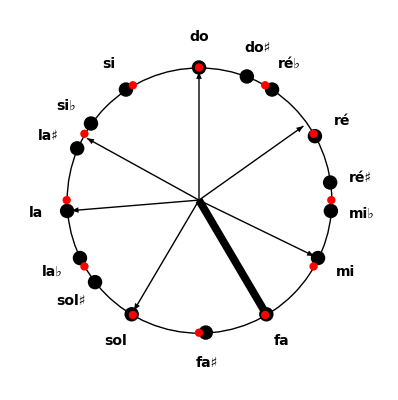

```mathematica
Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21quintes[[k]],Bold,FontSize->14],{(3.7+If[k==12,0,0]+If[k==13,0,0])Cos[theta[zarl16[[k-3]]]],3.7Sin[theta[zarl16[[k-3]]]]}],{k,4,19}],Table[Point[{3Cos[theta[zarl16[[k]]]],3Sin[theta[zarl16[[k]]]]}],{k,1,16}],Table[Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[k]]+zarl16ordonne[[j]]]],2.9Sin[theta[zarl16ordonne[[k]]+zarl16ordonne[[j]]]]}}],{k,{4,7,8,10,13,16}}],Thickness[0.014],Arrow[{{0,0},{2.9Cos[theta[zarl16ordonne[[j]]]],2.9Sin[theta[zarl16ordonne[[j]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
zarl[m_,n_]:=1200. (m Log[2,3]+n Log[2,5]-Floor[m Log[2,3]+n Log[2,5]])
```

```mathematica
Differences[Sort[Flatten[Table[zarl[m,n],{n,-1,2},{m,-1,2}]]]]
```

{70.6724,41.0589,92.1787,70.6724,41.0589,70.6724,111.731,92.1787,111.731,70.6724,41.0589,70.6724,92.1787,41.0589,70.6724}

```mathematica
Z=1200. Log[2,81/80];P=1200.Log[2,3^12/2^19];S=P-Z;
```

```mathematica
{td+P-2Z,3Z-P,td+P-Z,td+Z}
```

{70.6724,41.0589,92.1787,111.731}

```mathematica
Differences[Sort[Flatten[Table[zarl[m,n],{n,-2,3},{m,-2,3}]]]]
```

{70.6724,21.5063,19.5526,21.5063,29.6136,19.5526,21.5063,19.5526,51.1199,41.0589,70.6724,41.0589,29.6136,21.5063,19.5526,21.5063,49.1661,21.5063,19.5526,21.5063,29.6136,41.0589,70.6724,41.0589,51.1199,19.5526,21.5063,19.5526,29.6136,21.5063,19.5526,21.5063,70.6724,41.0589,29.6136}

```mathematica
DeleteDuplicates[%,Abs[#1-#2]<0.001&]
```

{70.6724,21.5063,19.5526,29.6136,51.1199,41.0589,49.1661}

```mathematica
{td+P-2Z,Z,2Z-P,td+2P-4Z,td+2P-5Z,3Z-P,td+P-3Z}
```

{70.6724,21.5063,19.5526,51.1199,29.6136,41.0589,49.1661}

```mathematica
zarl36=Flatten[Table[1200. Log[2,(3^m 5^n)/(2^Floor[Log[2,3^m 5^n]])],{n,-2,3},{m,-2,3}]]
```

{223.463,925.418,427.373,1129.33,631.283,133.238,609.776,111.731,813.686,315.641,1017.6,519.551,996.09,498.045,0.,701.955,203.91,905.865,182.404,884.359,386.314,1088.27,590.224,92.1787,568.717,70.6724,772.627,274.582,976.537,478.492,955.031,456.986,1158.94,660.896,162.851,864.806}

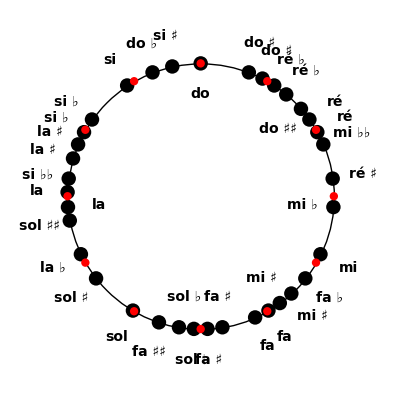

```mathematica
zarlino36=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes35quintes[[f[k]]],Bold,FontSize->14],(3+0.7 If[Mod[k,5]==0,-1,1]){Cos[theta[zarl36[[k]]]],Sin[theta[zarl36[[k]]]]}],{k,1,36}],Table[Point[{3Cos[theta[zarl36[[k]]]],3Sin[theta[zarl36[[k]]]]}],{k,1,36}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

## Modes anciens

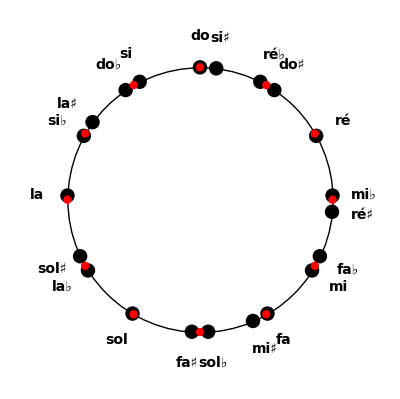

```mathematica
pythagore21=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
pyth[m_]:=1200.(m Log[2,3]-Floor[m Log[2,3]])
```

```mathematica
Differences[Sort[Table[pyth[m],{m,-8,12}]]]
```

{23.46,66.765,23.46,90.225,90.225,23.46,66.765,23.46,90.225,23.46,66.765,23.46,90.225,90.225,23.46,90.225,90.225,23.46,66.765,23.46}

```mathematica
{P,td-P,td}
```

{23.46,66.765,90.225}

```mathematica
Differences[Sort[Table[pyth[m],{m,-8,12}]]]
```

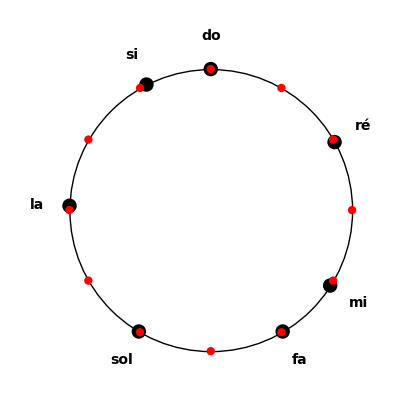

```mathematica
pyth7=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes35quintes[[k+16]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[k(3tc+4td)]],3.7Sin[theta[k(3tc+4td)]]}],{k,-1,5}],Table[Point[{3Cos[theta[k(3tc+4td)]],3Sin[theta[k(3tc+4td)]]}],{k,-1,5}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
pythagore21=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

-Graphics-

```mathematica
modeionien={T,T,td,T,T,T,td};modedorien=RotateLeft[modeionien,1];modephrygien=RotateLeft[modeionien,2];modelydien=RotateLeft[modeionien,3];modemyxolydien=RotateLeft[modeionien,4];modeeolien=RotateLeft[modeionien,5];modelocrien=RotateLeft[modeionien,6];
```

```mathematica
Clear[ionien];ionien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modeionien,touteslesnotes21[[n]]]]]],1200]]   (*positions des notes du mode ionien avec une tonique parmi les pyth21 : n=1->do etc*)
```

```mathematica
Clear[dorien];dorien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modedorien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
Clear[phrygien];phrygien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modephrygien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
Clear[lydien];lydien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modelydien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
Clear[myxolydien];myxolydien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modemyxolydien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
Clear[eolien];eolien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modeeolien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
Clear[locrien];locrien[n_]:=Chop[Mod[Most[Simplify[Accumulate[Prepend[modelocrien,touteslesnotes21[[n]]]]]],1200]]
```

```mathematica
modeancien[i_,n_]:=Which[i==1,ionien[n],i==2,dorien[n],i==3,phrygien[n],i==4,lydien[n],i==5,myxolydien[n],i==6,eolien[n],i==7,locrien[n]]
```

```mathematica
(*Affichage de la gamme démarrant sur la tonique n, 21 possibilités, dans mode ancien m, 7 possibilités m=1 ->ionien, etc*)  gamme[m_,n_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.9Cos[theta[modeancien[m,n][[k]]]],2.9Sin[theta[modeancien[m,n][[k]]]]}}],{k,2,7}],Thickness[0.014],Arrow[{{0,0},{2.9Cos[theta[modeancien[m,n][[1]]]],2.9Sin[theta[modeancien[m,n][[1]]]]}}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

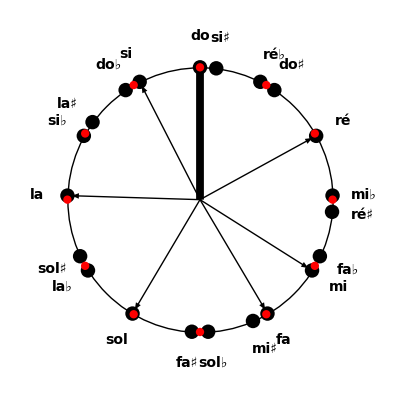

```mathematica
gamme[1,1]   (*gamme de si en mode lydien (n°4)*)
```

## ListAnimate marche bien

```mathematica
Clear[mode1];mode1=ListAnimate[Table[gamme[1,n],{n,1,21,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode de do (ionien)",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\pourmode1\\mode1.avi",mode1]
```

C:\wamp64\www\physinfo\videos\pourmode1\mode1.avi

## Gammes tempérées :

```mathematica
majeur={0,2,4,5,7,9,11};maj[k_,t_]:=100(majeur[[k]]+t);mineur={0,2,3,5,7,8,11};min[k_,t_]:=100(mineur[[k]]+t);
```

```mathematica
gammemajtemp[t_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[ maj[k,t]]],2.8Sin[theta[maj[k,t]]]}}],{k,2,7}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[maj[1,t]]],2.8Sin[theta[ maj[1,t]]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

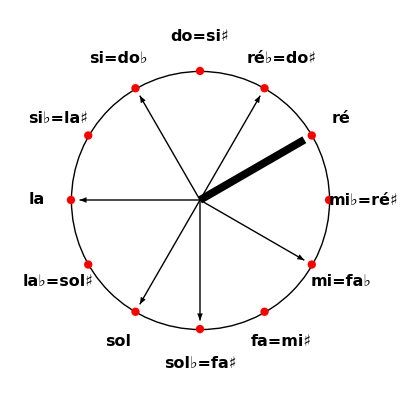

```mathematica
gammemajtemp[2]
```

```mathematica
modeM=ListAnimate[Table[gammemajtemp[t],{t,0,11,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode majeur",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\modeMaj.avi",modeM]
```

C:\wamp64\www\physinfo\videos\modes\modeMaj.avi

```mathematica
gammemintemp[t_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[ min[k,t]]],2.8Sin[theta[min[k,t]]]}}],{k,2,7}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[min[1,t]]],2.8Sin[theta[ min[1,t]]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
modemi=ListAnimate[Table[gammemintemp[t],{t,0,11,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode mineur harmonique",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\modemi.avi",modemi]
```

C:\wamp64\www\physinfo\videos\modes\modemi.avi

## Modes à transpositions limitées :

```mathematica
touslesmodestemperes=Sort[Flatten[Table[Flatten[Permutations[#]&/@Select[IntegerPartitions[12],Length[#]==k&],1],{k,12}],1]];
```

```mathematica
Length[touslesmodestemperes]
```

2048

```mathematica
numerodumode[x_]:=Flatten[Position[touslesmodestemperes,x]][[1]]
```

```mathematica
modenumero[x_]:=touslesmodestemperes[[x]]
```

```mathematica
modenumero[1361]
```

{2,2,1,2,2,2,1}

```mathematica
numerodumode[{2,2,1,2,2,2,1}]   (*Mode M*)
```

1361

```mathematica
numerodumode[{2,1,2,2,1,3,1}]   (*Mode m*)
```

1324

```mathematica
touteslesgammesdumodetempere=Table[Sort[Mod[Accumulate[100{2,2,1,2,2,2,1}]+100 k,1200]],{k,0,11}]
```

{{0,200,400,500,700,900,1100},{0,100,300,500,600,800,1000},{100,200,400,600,700,900,1100},{0,200,300,500,700,800,1000},{100,300,400,600,800,900,1100},{0,200,400,500,700,900,1000},{100,300,500,600,800,1000,1100},{0,200,400,600,700,900,1100},{0,100,300,500,700,800,1000},{100,200,400,600,800,900,1100},{0,200,300,500,700,900,1000},{100,300,400,600,800,1000,1100}}

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[1361]]]+100 k,1200]],{k,0,11}]]]   (*mode majeur*)
```

12

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[2048]]]+100 k,1200]],{k,0,11}]]]      (*mode dodécatonique*)
```

1

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[849]]]+100 k,1200]],{k,0,11}]]]      (*messiaen1 : mode par tons*)
```

2

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[1636]]]+100 k,1200]],{k,0,11}]]]      (*messiaen2 : mode octotonique*)
```

3

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[1954]]]+100 k,1200]],{k,0,11}]]]      (*messiaen3 : mode nonatonique*)
```

4

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[1594]]]+100 k,1200]],{k,0,11}]]]      (*messiaen4*)
```

6

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[741]]]+100 k,1200]],{k,0,11}]]]      (*messiaen5*)
```

6

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[1761]]]+100 k,1200]],{k,0,11}]]]      (*messiaen6*)
```

6

```mathematica
Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[2004]]]+100 k,1200]],{k,0,11}]]]      (*messiaen7*)
```

6

```mathematica
modesperiodiques={};Do[{z=DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[j]]]+100 k,1200]],{k,0,11}]],If[Length[z] <12,modesperiodiques=Append[modesperiodiques,{j,touslesmodestemperes[[j]],Length[z]}],Continue[]]},{j,1,2048}];modesperiodiques
```

{{7,{6,6},6},{43,{4,4,4},4},{98,{1,5,1,5},6},{135,{2,4,2,4},6},{164,{3,3,3,3},3},{186,{4,2,4,2},6},{202,{5,1,5,1},6},{627,{1,1,4,1,1,4},6},{684,{1,2,3,1,2,3},6},{712,{1,3,1,3,1,3},4},{720,{1,3,2,1,3,2},6},{741,{1,4,1,1,4,1},6},{813,{2,1,3,2,1,3},6},{849,{2,2,2,2,2,2},2},{870,{2,3,1,2,3,1},6},{921,{3,1,2,3,1,2},6},{926,{3,1,3,1,3,1},4},{942,{3,2,1,3,2,1},6},{978,{4,1,1,4,1,1},6},{1542,{1,1,1,3,1,1,1,3},6},{1578,{1,1,2,2,1,1,2,2},6},{1594,{1,1,3,1,1,1,3,1},6},{1636,{1,2,1,2,1,2,1,2},3},{1652,{1,2,2,1,1,2,2,1},6},{1674,{1,3,1,1,1,3,1,1},6},{1723,{2,1,1,2,2,1,1,2},6},{1739,{2,1,2,1,2,1,2,1},3},{1761,{2,2,1,1,2,2,1,1},6},{1790,{3,1,1,1,3,1,1,1},6},{1879,{1,1,2,1,1,2,1,1,2},4},{1912,{1,2,1,1,2,1,1,2,1},4},{1954,{2,1,1,2,1,1,2,1,1},4},{1997,{1,1,1,1,2,1,1,1,1,2},6},{2004,{1,1,1,2,1,1,1,1,2,1},6},{2012,{1,1,2,1,1,1,1,2,1,1},6},{2021,{1,2,1,1,1,1,2,1,1,1},6},{2031,{2,1,1,1,1,2,1,1,1,1},6},{2048,{1,1,1,1,1,1,1,1,1,1,1,1},1}}

```mathematica
Length[modesperiodiques]
```

38

```mathematica
modesperiodiquesbis={};Do[{z=DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[j]]]+100 k,1200]],{k,0,11}]],If[Length[z] <12,modesperiodiquesbis=Append[modesperiodiquesbis,{j,touslesmodestemperes[[j]]}],Continue[]]},{j,1,2048}];modesperiodiquesbis
```

```mathematica
{{7,{6,6}},{43,{4,4,4}},{98,{1,5,1,5}},{135,{2,4,2,4}},{164,{3,3,3,3}},{186,{4,2,4,2}},{202,{5,1,5,1}},{627,{1,1,4,1,1,4}},{684,{1,2,3,1,2,3}},{712,{1,3,1,3,1,3}},{720,{1,3,2,1,3,2}},{741,{1,4,1,1,4,1}},{813,{2,1,3,2,1,3}},{849,{2,2,2,2,2,2}},{870,{2,3,1,2,3,1}},{921,{3,1,2,3,1,2}},{926,{3,1,3,1,3,1}},{942,{3,2,1,3,2,1}},{978,{4,1,1,4,1,1}},{1542,{1,1,1,3,1,1,1,3}},{1578,{1,1,2,2,1,1,2,2}},{1594,{1,1,3,1,1,1,3,1}},{1636,{1,2,1,2,1,2,1,2}},{1652,{1,2,2,1,1,2,2,1}},{1674,{1,3,1,1,1,3,1,1}},{1723,{2,1,1,2,2,1,1,2}},{1739,{2,1,2,1,2,1,2,1}},{1761,{2,2,1,1,2,2,1,1}},{1790,{3,1,1,1,3,1,1,1}},{1879,{1,1,2,1,1,2,1,1,2}},{1912,{1,2,1,1,2,1,1,2,1}},{1954,{2,1,1,2,1,1,2,1,1}},{1997,{1,1,1,1,2,1,1,1,1,2}},{2004,{1,1,1,2,1,1,1,1,2,1}},{2012,{1,1,2,1,1,1,1,2,1,1}},{2021,{1,2,1,1,1,1,2,1,1,1}},{2031,{2,1,1,1,1,2,1,1,1,1}},{2048,{1,1,1,1,1,1,1,1,1,1,1,1}},{xxx},{xxx}}
```

```mathematica
Grid[Partition[{{7,{6,6}},{43,{4,4,4}},{98,{1,5,1,5}},{135,{2,4,2,4}},{164,{3,3,3,3}},{186,{4,2,4,2}},{202,{5,1,5,1}},{627,{1,1,4,1,1,4}},{684,{1,2,3,1,2,3}},{712,{1,3,1,3,1,3}},{720,{1,3,2,1,3,2}},{741,{1,4,1,1,4,1}},{813,{2,1,3,2,1,3}},{849,{2,2,2,2,2,2}},{870,{2,3,1,2,3,1}},{921,{3,1,2,3,1,2}},{926,{3,1,3,1,3,1}},{942,{3,2,1,3,2,1}},{978,{4,1,1,4,1,1}},{1542,{1,1,1,3,1,1,1,3}},{1578,{1,1,2,2,1,1,2,2}},{1594,{1,1,3,1,1,1,3,1}},{1636,{1,2,1,2,1,2,1,2}},{1652,{1,2,2,1,1,2,2,1}},{1674,{1,3,1,1,1,3,1,1}},{1723,{2,1,1,2,2,1,1,2}},{1739,{2,1,2,1,2,1,2,1}},{1761,{2,2,1,1,2,2,1,1}},{1790,{3,1,1,1,3,1,1,1}},{1879,{1,1,2,1,1,2,1,1,2}},{1912,{1,2,1,1,2,1,1,2,1}},{1954,{2,1,1,2,1,1,2,1,1}},{1997,{1,1,1,1,2,1,1,1,1,2}},{2004,{1,1,1,2,1,1,1,1,2,1}},{2012,{1,1,2,1,1,1,1,2,1,1}},{2021,{1,2,1,1,1,1,2,1,1,1}},{2031,{2,1,1,1,1,2,1,1,1,1}},{2048,{1,1,1,1,1,1,1,1,1,1,1,1}},Null,Null},4]]
```

{7,{6,6}} | {43,{4,4,4}} | {98,{1,5,1,5}} | {135,{2,4,2,4}}
{164,{3,3,3,3}} | {186,{4,2,4,2}} | {202,{5,1,5,1}} | {627,{1,1,4,1,1,4}}
{684,{1,2,3,1,2,3}} | {712,{1,3,1,3,1,3}} | {720,{1,3,2,1,3,2}} | {741,{1,4,1,1,4,1}}
{813,{2,1,3,2,1,3}} | {849,{2,2,2,2,2,2}} | {870,{2,3,1,2,3,1}} | {921,{3,1,2,3,1,2}}
{926,{3,1,3,1,3,1}} | {942,{3,2,1,3,2,1}} | {978,{4,1,1,4,1,1}} | {1542,{1,1,1,3,1,1,1,3}}
{1578,{1,1,2,2,1,1,2,2}} | {1594,{1,1,3,1,1,1,3,1}} | {1636,{1,2,1,2,1,2,1,2}} | {1652,{1,2,2,1,1,2,2,1}}
{1674,{1,3,1,1,1,3,1,1}} | {1723,{2,1,1,2,2,1,1,2}} | {1739,{2,1,2,1,2,1,2,1}} | {1761,{2,2,1,1,2,2,1,1}}
{1790,{3,1,1,1,3,1,1,1}} | {1879,{1,1,2,1,1,2,1,1,2}} | {1912,{1,2,1,1,2,1,1,2,1}} | {1954,{2,1,1,2,1,1,2,1,1}}
{1997,{1,1,1,1,2,1,1,1,1,2}} | {2004,{1,1,1,2,1,1,1,1,2,1}} | {2012,{1,1,2,1,1,1,1,2,1,1}} | {2021,{1,2,1,1,1,1,2,1,1,1}}
{2031,{2,1,1,1,1,2,1,1,1,1}} | {2048,{1,1,1,1,1,1,1,1,1,1,1,1}} |  |

```mathematica
modesperiodiques={};Do[If[Length[DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[j]]]+100 k,1200]],{k,0,11}]]] <12,modesperiodiques=Append[modesperiodiques,j],Continue[]],{j,1,2048}];modesperiodiques
```

{7,43,98,135,164,186,202,627,684,712,720,741,813,849,870,921,926,942,978,1542,1578,1594,1636,1652,1674,1723,1739,1761,1790,1879,1912,1954,1997,2004,2012,2021,2031,2048}

```mathematica
touslesmodesatranspositionslimitees=touslesmodestemperes[[#]]&/@modesperiodiques
```

```mathematica
{{6,6},{4,4,4},{1,5,1,5},{2,4,2,4},{3,3,3,3},{4,2,4,2},{5,1,5,1},{1,1,4,1,1,4},{1,2,3,1,2,3},{1,3,1,3,1,3},{1,3,2,1,3,2},{1,4,1,1,4,1},{2,1,3,2,1,3},{2,2,2,2,2,2},{2,3,1,2,3,1},{3,1,2,3,1,2},{3,1,3,1,3,1},{3,2,1,3,2,1},{4,1,1,4,1,1},{1,1,1,3,1,1,1,3},{1,1,2,2,1,1,2,2},{1,1,3,1,1,1,3,1},{1,2,1,2,1,2,1,2},{1,2,2,1,1,2,2,1},{1,3,1,1,1,3,1,1},{2,1,1,2,2,1,1,2},{2,1,2,1,2,1,2,1},{2,2,1,1,2,2,1,1},{3,1,1,1,3,1,1,1},{1,1,2,1,1,2,1,1,2},{1,2,1,1,2,1,1,2,1},{2,1,1,2,1,1,2,1,1},{1,1,1,1,2,1,1,1,1,2},{1,1,1,2,1,1,1,1,2,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,1,1,1,2,1,1,1},{2,1,1,1,1,2,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}
```

```mathematica
Length[%]  (*soit 38 modes au total, 31 si on exclut les 7 modes comportant moins de 5 notes*)
```

38

```mathematica
modesperiodiques={};Do[{z=DeleteDuplicates[Table[Sort[Mod[Accumulate[100touslesmodestemperes[[j]]]+100 k,1200]],{k,0,11}]],If[Length[z] <12,modesperiodiques=Append[modesperiodiques,touslesmodestemperes[[j]]],Continue[]]},{j,1,2048}];Drop[modesperiodiques,7]
```

{{1,1,4,1,1,4},{1,2,3,1,2,3},{1,3,1,3,1,3},{1,3,2,1,3,2},{1,4,1,1,4,1},{2,1,3,2,1,3},{2,2,2,2,2,2},{2,3,1,2,3,1},{3,1,2,3,1,2},{3,1,3,1,3,1},{3,2,1,3,2,1},{4,1,1,4,1,1},{1,1,1,3,1,1,1,3},{1,1,2,2,1,1,2,2},{1,1,3,1,1,1,3,1},{1,2,1,2,1,2,1,2},{1,2,2,1,1,2,2,1},{1,3,1,1,1,3,1,1},{2,1,1,2,2,1,1,2},{2,1,2,1,2,1,2,1},{2,2,1,1,2,2,1,1},{3,1,1,1,3,1,1,1},{1,1,2,1,1,2,1,1,2},{1,2,1,1,2,1,1,2,1},{2,1,1,2,1,1,2,1,1},{1,1,1,1,2,1,1,1,1,2},{1,1,1,2,1,1,1,1,2,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,1,1,1,2,1,1,1},{2,1,1,1,1,2,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
messiaen=touslesmodestemperes[[#]]&/@{849,1636,1879,1542,627,1578,1997}
```

{{2,2,2,2,2,2},{1,2,1,2,1,2,1,2},{1,1,2,1,1,2,1,1,2},{1,1,1,3,1,1,1,3},{1,1,4,1,1,4},{1,1,2,2,1,1,2,2},{1,1,1,1,2,1,1,1,1,2}}

```mathematica
messiaenplus2=Join[touslesmodestemperes[[#]]&/@{849,1636,1879,1542,627,1578,1997},{{1,3,1,3,1,3},{1,2,3,1,2,3}}]
```

{{2,2,2,2,2,2},{1,2,1,2,1,2,1,2},{1,1,2,1,1,2,1,1,2},{1,1,1,3,1,1,1,3},{1,1,4,1,1,4},{1,1,2,2,1,1,2,2},{1,1,1,1,2,1,1,1,1,2},{1,3,1,3,1,3},{1,2,3,1,2,3}}

```mathematica
transpo[x_]:=Union[Table[RotateLeft[x,j],{j,0,Length[x]-1}]]
```

```mathematica
transpo[{1,3,1,3}]
```

{{1,3,1,3},{3,1,3,1}}

```mathematica
touteslestranspodemessiaenplus2=Flatten[transpo/@messiaenplus2 ,1]                        (*à revoir, semble ok !!!*)
```

{{2,2,2,2,2,2},{1,2,1,2,1,2,1,2},{2,1,2,1,2,1,2,1},{1,1,2,1,1,2,1,1,2},{1,2,1,1,2,1,1,2,1},{2,1,1,2,1,1,2,1,1},{1,1,1,3,1,1,1,3},{1,1,3,1,1,1,3,1},{1,3,1,1,1,3,1,1},{3,1,1,1,3,1,1,1},{1,1,4,1,1,4},{1,4,1,1,4,1},{4,1,1,4,1,1},{1,1,2,2,1,1,2,2},{1,2,2,1,1,2,2,1},{2,1,1,2,2,1,1,2},{2,2,1,1,2,2,1,1},{1,1,1,1,2,1,1,1,1,2},{1,1,1,2,1,1,1,1,2,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,1,1,1,2,1,1,1},{2,1,1,1,1,2,1,1,1,1},{1,3,1,3,1,3},{3,1,3,1,3,1},{1,2,3,1,2,3},{2,3,1,2,3,1},{3,1,2,3,1,2}}

```mathematica
moden1={0,200,400,600,800,1000,200};
```

```mathematica
Clear[m1];m1=Chop[Mod[Most[Simplify[Accumulate[moden1]]],1200]]   (*positions des notes du mode n°1 sur la gamme chromatique*)
```

{200,400,600,800,1000}

```mathematica
notes12[[1]]
```

do=si♯

```mathematica
Table[FreeQ[touteslestranspodemessiaenplus2,Drop[modesperiodiques,7][[j]]],{j,1,31}]
```

{False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True}

```mathematica
Table[Drop[modesperiodiques,7][[j]],{j,{4,6,11,31}}]
```

{{1,3,2,1,3,2},{2,1,3,2,1,3},{3,2,1,3,2,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

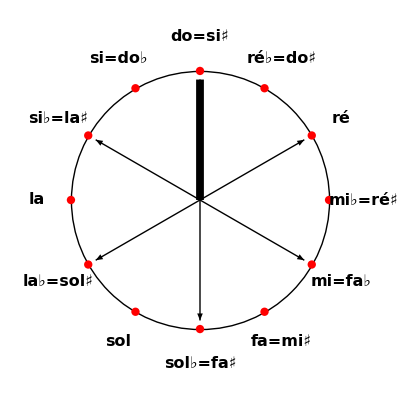

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[200k]],2.8Sin[theta[200k]]}}],{k,2,7}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[0]],2.8Sin[theta[0]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],3.8{Cos[theta[100(k-1)]],Sin[theta[100(k-1)]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
gammepartons[t_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[200k+100t]],2.8Sin[theta[200k+100t]]}}],{k,2,7}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[200 0+100t]],2.8Sin[ theta[200 0+100t]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
modepartons=ListAnimate[Table[gammepartons[t],{t,0,11,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode par tons",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\modepartons.avi",modepartons]
```

C:\wamp64\www\physinfo\videos\modes\modepartons.avi

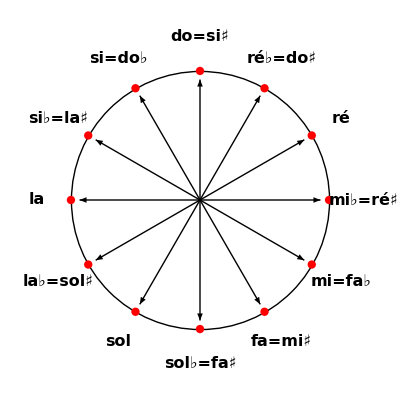

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[noteschromatiques[[k]]]],2.8Sin[theta[noteschromatiques[[k]]]]}}],{k,12}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[noteschromatiques[[k]]]],3.8Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
gamme12[t_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[100k+100t]],2.8Sin[theta[100k+100t]]}}],{k,1,11}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[100 0+100t]],2.8Sin[ theta[100 0+100t]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
mode12=ListAnimate[Table[gamme12[t],{t,0,11,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None,"Mode à 12 sons",None},LabelStyle->{Bold,Medium}]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\mode12.avi",mode12]
```

C:\wamp64\www\physinfo\videos\modes\mode12.avi

## Systématisation des gammes à transpositions limitées

```mathematica
schema=touslesmodestemperes[[1361]];
```

```mathematica
Clear[interv];interv[n_]:=Most[Accumulate[Prepend[touslesmodestemperes[[n]],0]]]
```

```mathematica
mod[n_,k_,t_]:=100(interv[n][[k]]+t);
```

```mathematica
gamme[n_,t_]:=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[ mod[n,k,t]]],2.8Sin[theta[mod[n,k,t]]]}}],{k,2,Length[interv[n]]}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[mod[n,1,t]]],2.8Sin[theta[ mod[n,1,t]]]}}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
Clear[mode];mode[n_]:=ListAnimate[Table[gamme[n,t],{t,0,11,1}],AnimationRate->1,AnimationRepetitions->1,FrameLabel->{None,None, touslesmodestemperes[[n]],None},LabelStyle->{Bold,Medium}]
```

```mathematica
mode[1578]
```

```mathematica
Export["C:\\wamp64\\www\\physinfo\\videos\\modes\\mode1578.avi",mode[1578]]
```

C:\wamp64\www\physinfo\videos\modes\mode1578.avi

```mathematica
ecart=Table[RandomReal[{-20,20}],{j,12}]
```

{19.9647,4.64075,14.2987,19.6794,-12.0074,-8.37404,-13.7473,2.13994,-13.2005,17.7256,5.22172,-1.10731}

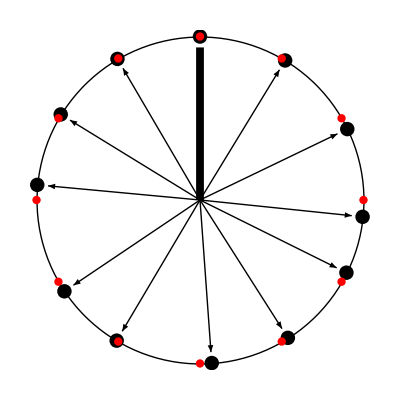

```mathematica
g1=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Point[{3Cos[theta[noteschromatiques[[k]]+If[k==1,0,1]ecart[[k]]]],3Sin[theta[noteschromatiques[[k]]+If[k==1,0,1]ecart[[k]]]]}],{k,1,12}],Table[Arrow[{{0,0},{2.8Cos[theta[noteschromatiques[[k]]+ecart[[k]]]],2.8Sin[theta[noteschromatiques[[k]]+ecart[[k]]]]}}],{k,2,12}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[noteschromatiques[[1]]]],2.8Sin[theta[noteschromatiques[[1]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

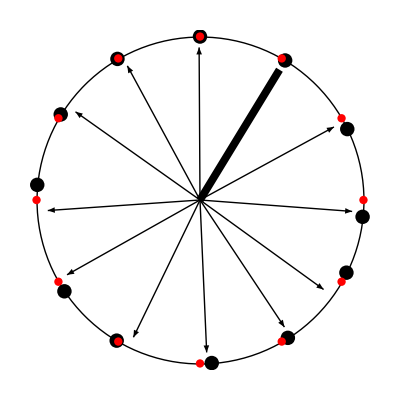

```mathematica
g2=Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Point[{3Cos[theta[noteschromatiques[[k]]+If[k==1,0,1]ecart[[k]]]],3Sin[theta[noteschromatiques[[k]]+If[k==1,0,1]ecart[[k]]]]}],{k,1,12}],Table[Arrow[{{0,0},{2.8Cos[theta[noteschromatiques[[2]]+noteschromatiques[[k]]+ecart[[k]]]],2.8Sin[theta[noteschromatiques[[2]]+noteschromatiques[[k]]+ecart[[k]]]]}}],{k,2,12}],Thickness[0.014],Arrow[{{0,0},{2.8Cos[theta[noteschromatiques[[2]]+ecart[[2]]]],2.8Sin[theta[noteschromatiques[[2]]+ecart[[2]]]]}}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
{g1,g2}
```

{-Graphics-,-Graphics-}

## Gamme harmonique :

```mathematica
harm=Table[Prime[m]/2^Floor[Log[2,Prime[m]]],{m,1,8}]
```

{1,3/2,5/4,7/4,11/8,13/8,17/16,19/16}

```mathematica
1200. Log[2,#]&/@harm
```

{0.,701.955,386.314,968.826,551.318,840.528,104.955,297.513}

```mathematica
Table[m/2^Floor[Log[2,m]],{m,1,19}]
```

{1,1,3/2,1,5/4,3/2,7/4,1,9/8,5/4,11/8,3/2,13/8,7/4,15/8,1,17/16,9/8,19/16}

```mathematica
DeleteDuplicates[Table[m/2^Floor[Log[2,m]],{m,1,19}]]
```

{1,3/2,5/4,7/4,9/8,11/8,13/8,15/8,17/16,19/16}

```mathematica
1200. Log[2,#]&/@{1,3/2,5/4,7/4,9/8,11/8,13/8,15/8,17/16,19/16}
```

{0.,701.955,386.314,968.826,203.91,551.318,840.528,1088.27,104.955,297.513}

```mathematica
Differences[Sort[1200. Log[2,#]&/@DeleteDuplicates[Table[m/2^Floor[Log[2,m]],{m,1,39}]]]]    (*Ces intervalles ne se déduisant pas d'un petit nombre d'intervalles élémentaires, la gamme harmonique est non transposable. C'est la conséquence du fait qu'elle résulte d'une construction arithmétique et non géométrique*)
```

{53.2729,51.6825,50.1842,48.7704,47.434,46.169,44.9696,43.8311,84.4672,80.537,76.9564,73.6807,70.6724,67.9002,65.3373,62.9609,60.7513,58.6915,56.7669}

```mathematica
Int[m_]:=1200. Log[2,m/2^Floor[Log[2,m]]]
```

```mathematica
Table[Int[m],{m,1,19}]
```

{0.,0.,701.955,0.,386.314,701.955,968.826,0.,203.91,386.314,551.318,701.955,840.528,968.826,1088.27,0.,104.955,203.91,297.513}

```mathematica
Int[19]
```

297.513

```mathematica
1200.(Log[2,19]-Floor[Log[2,19]])
```

297.513

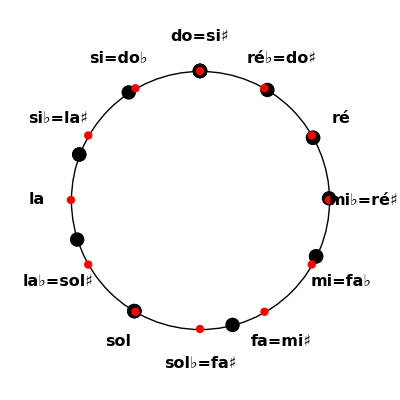

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[(k-1)100]],3.8Sin[theta[(k-1)100]]}],{k,1,12}],Table[Point[{3Cos[theta[Int[m]]],3Sin[theta[Int[m]]]}],{m,1,19}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

```mathematica
Table[Point[{3Cos[theta[Int[m]]],3Sin[theta[Int[m]]]}]
```